# Unfolding Pattern Search

## Global Functions

```mathematica
ClearAll["Global`*"]
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-λ IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

## General Reduction Patterns

```mathematica
ClearAll[ReductionPowers]

(*Function to compute the "leading power of λ" for an entry*)
LeadingPower[expr_,λ_]:=Module[{num,den, numExp, denExp},
num=Numerator[Together[expr]];
den=Denominator[Together[expr]];
numExp = Exponent[num,λ];
denExp = Exponent[den,λ];
{numExp - denExp, numExp, denExp}
];

(*Run reductions on all graphs of size n*)
ReductionPowers[n_,m_]:=Module[{graphs},
graphs=GraphData/@GraphData["Connected",n];
Flatten[
Table[
Module[{adjmat,powers,numExp,denExp},
adjmat=Simplify[Smash[graphs[[i]],S]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
<|
"GraphIndex"->i,
"Vertices"->S,
"reduction"->adjmat,
"Powers"->powers,
"NumExp"->numExp,
"DenExp"->denExp
|>
],
{i,Length[graphs]},
{S,Subsets[Range[n],{m}]}
],
1
]
];
```

```mathematica
data=ReductionPowers[3,1];

Length[data]   (*should be (#graphs×n) reductions*)
data[[1]]
```

6

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-1+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>

```mathematica
data=ReductionPowers[4,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

24

{{-1,24}}

{{1,13},{0,5},{2,6}}

{{2,13},{1,5},{3,6}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>

```mathematica
data=ReductionPowers[5,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

105

{{-1,105}}

{{3,22},{2,41},{1,34},{0,8}}

{{4,22},{3,41},{2,34},{1,8}}

<|GraphIndex→1,Vertex→v,reduction→{{(λ (-1+2 λ^2))/(1-3 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[6,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

672

{{-1,672}}

{{3,235},{2,226},{1,68},{4,135},{0,8}}

{{4,235},{3,226},{2,68},{5,135},{1,8}}

<|GraphIndex→1,Vertex→v,reduction→{{(λ (-1+2 λ^2))/(2-5 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[7,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

5971

{{-1,5971}}

{{3,1650},{2,683},{1,152},{4,2003},{5,1469},{0,14}}

{{4,1650},{3,683},{2,152},{5,2003},{6,1469},{1,14}}

<|GraphIndex→1,Vertex→v,reduction→{{(2 λ (-1+λ^2))/(4-6 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[8,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

5904

{{-1,5904}}

{{4,1239},{3,956},{2,431},{5,1245},{6,1885},{1,138},{0,10}}

{{5,1239},{4,956},{3,431},{6,1245},{7,1885},{2,138},{1,10}}

<|GraphIndex→1,Vertex→v,reduction→{{(2 (6-6 λ^2+λ^4))/(λ (9-8 λ^2+λ^4))}},Powers→{-1},NumExp→{4},DenExp→{5}|>

```mathematica
(*All connected graphs on 4 vertices,reducing on every 2-vertex subset*)
data=ReductionPowers[3,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

6

{{-∞,2},{0,10},{-1,12}}

{{-∞,2},{0,16},{1,6}}

{{0,6},{1,18}}

<|GraphIndex→1,Vertex→v,reduction→{{0,1},{1,1/λ}},Powers→{-∞,0,0,-1},NumExp→{-∞,0,0,0},DenExp→{0,0,0,1}|>

```mathematica
data=ReductionPowers[4,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

36

{{-1,86},{-∞,6},{0,50},{-2,2}}

{{1,58},{-∞,6},{0,70},{2,10}}

{{2,44},{0,20},{1,80}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-1+λ^2),λ/(-1+λ^2)},{λ/(-1+λ^2),λ/(-1+λ^2)}},Powers→{-1,-1,-1,-1},NumExp→{1,1,1,1},DenExp→{2,2,2,2}|>

```mathematica
data=ReductionPowers[5,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

210

{{-1,542},{0,260},{-2,18},{-∞,18},{-3,2}}

{{1,351},{2,262},{0,177},{-∞,18},{3,32}}

{{2,401},{3,188},{1,189},{0,62}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-2+λ^2),1+1/(-2+λ^2)},{1+1/(-2+λ^2),(-1+λ^2)/(λ (-2+λ^2))}},Powers→{-1,0,0,-1},NumExp→{1,2,2,2},DenExp→{2,2,2,3}|>

```mathematica
data=ReductionPowers[6,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

```mathematica
1680
```

1680

```mathematica
data=ReductionPowers[4,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

24

{{-1,76},{-∞,40},{0,100}}

{{0,134},{-∞,40},{1,42}}

{{1,118},{0,98}}

<|GraphIndex→1,Vertex→v,reduction→{{1/λ,1/λ,1/λ},{1/λ,1/λ,1/λ},{1/λ,1/λ,1/λ}},Powers→{-1,-1,-1,-1,-1,-1,-1,-1,-1},NumExp→{0,0,0,0,0,0,0,0,0},DenExp→{1,1,1,1,1,1,1,1,1}|>

```mathematica
data=ReductionPowers[5,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

210

{{-1,864},{0,780},{-∞,208},{-2,38}}

{{1,662},{0,910},{-∞,208},{2,110}}

{{2,422},{0,490},{1,978}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-1+λ^2),1,λ/(-1+λ^2)},{1,0,1},{λ/(-1+λ^2),1,λ/(-1+λ^2)}},Powers→{-1,0,-1,0,-∞,0,-1,0,-1},NumExp→{1,0,1,0,-∞,0,1,0,1},DenExp→{2,0,2,0,0,0,2,0,2}|>

```mathematica
data=ReductionPowers[6,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

2240

{{-1,10378},{0,7608},{-2,710},{-∞,1394},{-3,70}}

{{2,5644},{1,7246},{0,5038},{-∞,1394},{3,838}}

{{3,3520},{2,8942},{0,3086},{1,4612}}

<|GraphIndex→1,Vertex→v,reduction→{{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)},{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)},{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)}},Powers→{-1,-1,-1,-1,-1,-1,-1,-1,-1},NumExp→{2,2,2,2,2,2,2,2,2},DenExp→{3,3,3,3,3,3,3,3,3}|>

## Same Reduction Finding

```mathematica
ClearAll[ReductionPowers]

(*Function to compute the "leading power of λ" for an entry*)
LeadingPower[expr_,λ_]:=Module[{num,den, numExp, denExp},
num=Numerator[Together[expr]];
den=Denominator[Together[expr]];
numExp = Exponent[num,λ];
denExp = Exponent[den,λ];
{numExp - denExp, numExp, denExp}
];

(*Run reductions on all graphs of size n*)
ReductionPowers[n_,m_]:=Module[{graphs},
graphs=GraphData/@GraphData["Connected",n];
Flatten[
Table[
Module[{adjmat,key,powers,numExp,denExp},
adjmat=Simplify[Smash[graphs[[i]],S]];
(*canonicalize matrix form for comparison*)
key=Simplify[Normal[adjmat]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
<|
"n"->n,
"GraphIndex"->i,
"Vertices"->S,
"Reduction"->key,
"Powers"->powers,
"NumExp"->numExp,
"DenExp"->denExp
|>
],
{i,Length[graphs]},
{S,Subsets[Range[n],{m}]}
],
1
]
];
```

## Single Vertex Reduction Matching

```mathematica
data=Flatten@Table[ReductionPowers[n,1],{n,4,8}];
sameReductions=GroupBy[data,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&];
matches=Select[sameReductions,Length[#]>1&];
data // Length (*how many original graphs there are*)
Length[matches]     (*how many unique reductions appear in multiple graphs*)
matches[[1]]                  (*look at one reduction’s equivalence class*)
```

12676

2894

{<|n→4,GraphIndex→1,Vertices→{1}|>,<|n→4,GraphIndex→1,Vertices→{2}|>,<|n→4,GraphIndex→1,Vertices→{3}|>}

=== Match 1 ===

Reduction matrix:

(λ/(-2+λ^2))

n = 4, GraphIndex = 1, Vertices = {1}

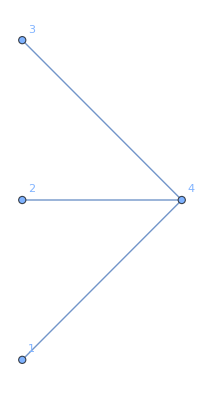

n = 4, GraphIndex = 1, Vertices = {2}

-Graphics-

n = 4, GraphIndex = 1, Vertices = {3}

-Graphics-

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[matches][[i]];(*the shared reduction matrix*)
group=matches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Min[1,Length[matches]]}
]
```

```mathematica
filteredMatches=Select[
matches,
Module[{group=#,ns,ids},
ns=group[[All,"n"]];
ids=group[[All,"GraphIndex"]];
(Length[DeleteDuplicates[Transpose[{ns,ids}]]]>1)
]&
];
Length[filteredMatches]
```

120

=== Match 1 ===

Reduction matrix:

(-(2 λ)/(2+λ-λ^2))

n = 4, GraphIndex = 2, Vertices = {1}

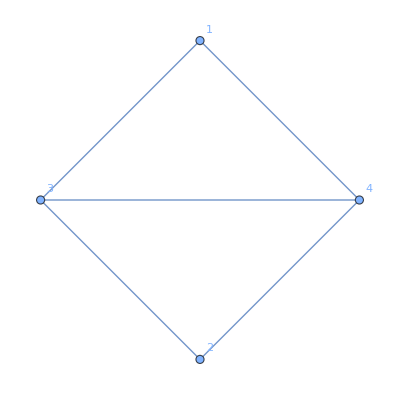

n = 4, GraphIndex = 2, Vertices = {2}

-Graphics-

n = 7, GraphIndex = 638, Vertices = {1}

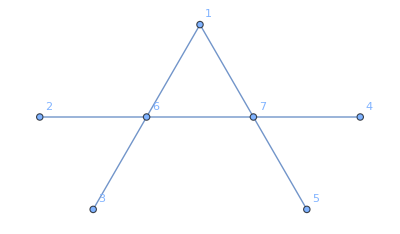

=== Match 2 ===

Reduction matrix:

((2 λ)/(-2+λ^2))

n = 4, GraphIndex = 5, Vertices = {1}

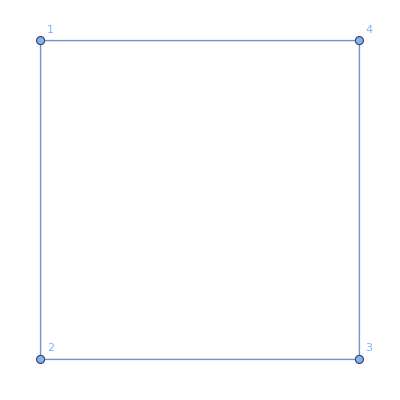

n = 4, GraphIndex = 5, Vertices = {2}

-Graphics-

n = 4, GraphIndex = 5, Vertices = {3}

-Graphics-

n = 4, GraphIndex = 5, Vertices = {4}

-Graphics-

n = 7, GraphIndex = 575, Vertices = {1}

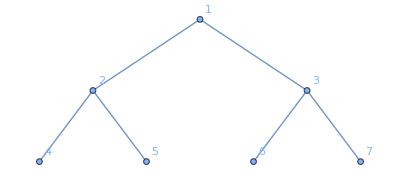

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[filteredMatches][[i]];(*the shared reduction matrix*)
group=filteredMatches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Min[2,Length[filteredMatches]]}
]
```

## Single Vertex Reduction Examples

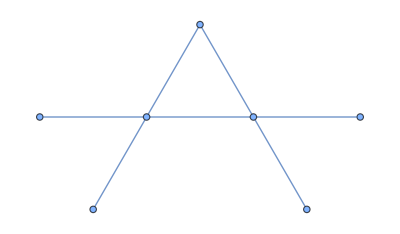

{{-(2 λ)/(2+λ-λ^2)}}

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[638]]
Simplify[Smash[g,{1}]]
```

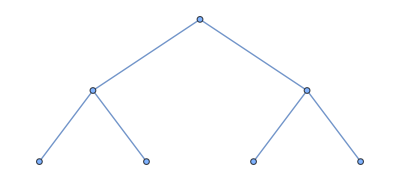

{{(2 λ)/(-2+λ^2)}}

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[575]]
Simplify[Smash[g,{1}]]
```

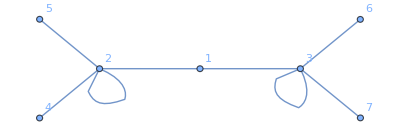

{{-(2 λ)/(2+λ-λ^2)}}

```mathematica
graph=G = Graph[{1<->2, 1<->3,2<->2,2<->4,2<->5,3<->3,3<->6,3<->7}, VertexLabels->"Name"]
Simplify[Smash[graph,{1}]]
```

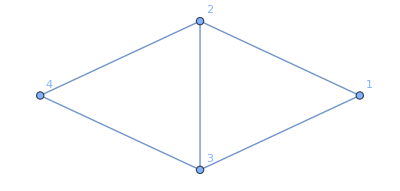

{{λ/(-1+λ^2),λ/(-1+λ)},{λ/(-1+λ),2/(-1+λ)}}

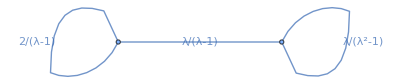

```mathematica
graph=G = Graph[{1<->2,1<->3,2<->3,2<->4,3<->4}, VertexLabels->"Name"]
adjmat=Simplify[Smash[graph,{1,2}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{λ/(-2+λ^2),(-2+λ+λ^2)/(-2+λ^2)},{(-2+λ+λ^2)/(-2+λ^2),(4-3 λ^2)/(2 λ-λ^3)}}

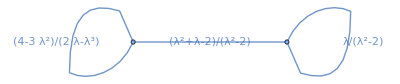

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[638]];
Print[Graph[g,VertexLabels->"Name"]];
adjmat=Simplify[Smash[g,{1,6}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

```mathematica
Simplify[x/(x^2-2)+((x^2+x-2)/(x^2-2))^2(3x^2-4)/(x^3-2x)]
```

(x (-2+x^2)+((-2+x+x^2)^2 (-4+3 x^2))/(-2 x+x^3))/((-2+x^2)^2)

## Double Vertex Reduction Matching

```mathematica
data=Flatten@Table[ReductionPowers[n,2],{n,4,8}];
sameReductions=GroupBy[data,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&];
matches=Select[sameReductions,Length[#]>1&];
data // Length (*how many original graphs there are*)
Length[matches]     (*how many unique reductions appear in multiple graphs*)
matches[[1]]
```

40503

8342

{<|n→4,GraphIndex→1,Vertices→{1,2}|>,<|n→4,GraphIndex→1,Vertices→{1,3}|>,<|n→4,GraphIndex→1,Vertices→{2,3}|>}

```mathematica
filteredMatches=Select[
matches,
Module[{group=#,ns,ids},
ns=group[[All,"n"]];
ids=group[[All,"GraphIndex"]];
(Length[DeleteDuplicates[Transpose[{ns,ids}]]]>1)
]&
];
Length[filteredMatches]
```

78

=== Match 1 ===

Reduction matrix:

((2 λ)/(-2+λ^2) | (2 λ)/(-2+λ^2)
(2 λ)/(-2+λ^2) | (2 λ)/(-2+λ^2))

n = 5, GraphIndex = 5, Vertices = {3, 4}

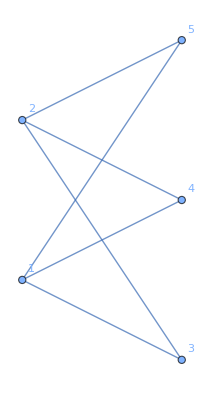

n = 5, GraphIndex = 5, Vertices = {3, 5}

-Graphics-

n = 5, GraphIndex = 5, Vertices = {4, 5}

-Graphics-

n = 8, GraphIndex = 333, Vertices = {2, 3}

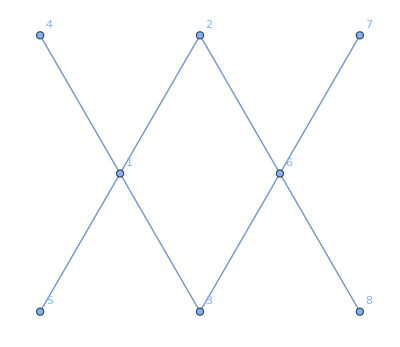

=== Match 2 ===

Reduction matrix:

((-3+2 λ+3 λ^2)/(λ (-2+λ^2)) | (-1+2 λ+2 λ^2)/(λ (-2+λ^2))
(-1+2 λ+2 λ^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

n = 6, GraphIndex = 47, Vertices = {4, 5}

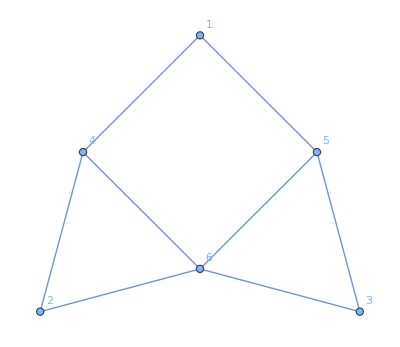

n = 7, GraphIndex = 668, Vertices = {5, 6}

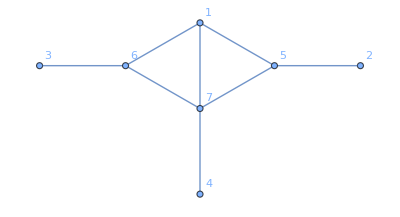

=== Match 3 ===

Reduction matrix:

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

n = 6, GraphIndex = 47, Vertices = {4, 6}

-Graphics-

n = 6, GraphIndex = 47, Vertices = {5, 6}

-Graphics-

n = 7, GraphIndex = 668, Vertices = {5, 7}

-Graphics-

n = 7, GraphIndex = 668, Vertices = {6, 7}

-Graphics-

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[filteredMatches][[i]];(*the shared reduction matrix*)
group=filteredMatches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Min[3,Length[filteredMatches]]}
]
```

## Double Vertex Reduction Examples

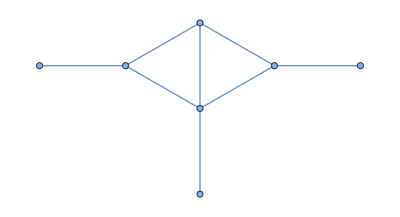

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[668]]
MatrixForm[Simplify[Smash[g,{5,7}]]]
```